```mathematica
q = ({{-1, 1/(2+k), k/(2+k), 1/(2+k)}, {1/(2+k), -1, 1/(2+k), k/(2+k)}, {k/(2+k), 1/(2+k), -1, 1/(2+k)}, {1/(2+k), k/(2+k), 1/(2+k), -1}})
MatrixExp[q t]
```

{{-1,1/(2+k),k/(2+k),1/(2+k)},{1/(2+k),-1,1/(2+k),k/(2+k)},{k/(2+k),1/(2+k),-1,1/(2+k)},{1/(2+k),k/(2+k),1/(2+k),-1}}

{{1/4+1/4 ⅇ^(-(4 t)/(2+k))+1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k))),1/4+1/4 ⅇ^(-(4 t)/(2+k))-1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k)))},{1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k))),1/4+1/4 ⅇ^(-(4 t)/(2+k))+1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k))),1/4+1/4 ⅇ^(-(4 t)/(2+k))-1/2 ⅇ^(-(2 (1+k) t)/(2+k))},{1/4+1/4 ⅇ^(-(4 t)/(2+k))-1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k))),1/4+1/4 ⅇ^(-(4 t)/(2+k))+1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k)))},{1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k))),1/4+1/4 ⅇ^(-(4 t)/(2+k))-1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k))),1/4+1/4 ⅇ^(-(4 t)/(2+k))+1/2 ⅇ^(-(2 (1+k) t)/(2+k))}}

```mathematica
1
```

```mathematica
k =.
t =.
Simplify[1/4+1/4 ⅇ^(-(4 t)/(2+k))+1/2 ⅇ^(-(2 (1+k) t)/(2+k))]
Simplify[1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k)))]
Simplify[1/4+1/4 ⅇ^(-(4 t)/(2+k))-1/2 ⅇ^(-(2 (1+k) t)/(2+k))]
```

1/4 (1+ⅇ^(-(4 t)/(2+k))+2 ⅇ^(-(2 (1+k) t)/(2+k)))

1/4-1/4 ⅇ^(-(4 t)/(2+k))

1/4 (1+ⅇ^(-(4 t)/(2+k))-2 ⅇ^(-(2 (1+k) t)/(2+k)))

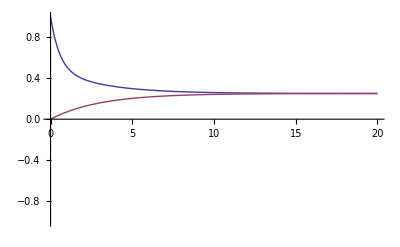

```mathematica
Plot[{1/4+1/4 ⅇ^(-(4 t)/(2+k))+1/2 ⅇ^(-(2 (1+k) t)/(2+k)),1/4 ⅇ^(-(4 t)/(2+k)) (-1+ⅇ^((4 t)/(2+k)))},{t,0,2*k}, PlotRange->1]
```

```mathematica
Simplify[MatrixExp[{{-1, 1},{1,-1}} t ]]
```

{{1/2 (1+ⅇ^(-2 t)),1/2-ⅇ^(-2 t)/2},{1/2-ⅇ^(-2 t)/2,1/2 (1+ⅇ^(-2 t))}}

```mathematica
t=0.01
1/2 (1+ⅇ^(-2 t))
1/2 (1-ⅇ^(-2 t))
```

0.01

0.990099

0.00990066